```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
```

```mathematica
ClearGlobal[]
```

```mathematica
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
RemoveGlobal[]
```

# Symmetric Three-Strategy Games

## The Model

### Various Payoff Matrices

```mathematica
(* Rock-Paper-Scissors *)
table1 = {{"", "O", "Y", "B"}, {"O", ε, -1, 1}, {"Y", 1, ε, -1}, {"B", -1, 1, ε}}
```

{{,O,Y,B},{O,ε,-1,1},{Y,1,ε,-1},{B,-1,1,ε}}

Some other games:

```mathematica
(* Maynard Smith' Hawk-Dove-Retaliator: Table 2a, p. 18 *) 
table2a ={{"", "H", "D", "R"}, {"H", -1, 2, -1}, {"D", 0, 1, 1}, {"R", -1, 1, 1}}
```

{{,H,D,R},{H,-1,2,-1},{D,0,1,1},{R,-1,1,1}}

```mathematica
(* Maynard Smith' Modified Hawk-Dove-Retaliator Table 2b, p. 18 *) 
table2b ={{"", "H", "D", "R"}, {"H", -1, 2, -1}, {"D", 0, 1, 0.9}, {"R", -1, 1.1, 1}}
```

{{,H,D,R},{H,-1,2,-1},{D,0,1,0.9},{R,-1,1.1,1}}

Let’s take the standard Hawk-Dove game and extend it with 50-50 “Mixed” strategy. I start with filling out the first two values in the  “M” row. The payoff to the mixed strategist when the opponent plays hawk is simply average of the first two cells in the “H” column, since the mixed strategist chooses either strategy with probability 50%. Same logic applies to “D” column. By symmetry, the first two values in the “M” column are row-averages of the corresponding “H” and “D” values. All that remains is to fill out the last cell, when mixed strategist plays against another mixed strategist. The payoff to either player is then equal to the average across the entire 2×2 table.

```mathematica
(* Hawk-Dove with a mixed strategy *) 
table3 ={{"", "H", "D", "M"}, {"H", -1, 2, 0.5}, {"D", 0, 1, 0.5}, {"M", -0.5, 1.5, 0.5}}
```

{{,H,D,M},{H,-1,2,0.5},{D,0,1,0.5},{M,-0.5,1.5,0.5}}

```mathematica
(* Hawk-Dove-Bully *) 
table4 ={{"", "H", "D", "B"}, {"H", -1, 2, 2}, {"D", 0, 1, 0}, {"B", 0, 2, 1}}
```

{{,H,D,B},{H,-1,2,2},{D,0,1,0},{B,0,2,1}}

```mathematica
(* Hawk-Dove-Bourgeois (Simple) *) 
table5a ={{"", "H", "D", "B"}, {"H", -1, 4, 1.5}, {"D", 0, 1, 0.5}, {"B", -0.5, 2.5, 2}}
```

{{,H,D,B},{H,-1,4,1.5},{D,0,1,0.5},{B,-0.5,2.5,2}}

```mathematica
(* Hawk-Dove-Bourgeois (Full) *) 
table5b ={{"", "H", "D", "B"}, {"H", (V-C)/2, V, (3V-C)/4}, {"D", 0, V/2, V/4}, {"B", (V-C)/4, 3V/4, V/2}}/.{V->2.0, C->4.0}
```

{{,H,D,B},{H,-1.,2.,0.5},{D,0,1.,0.5},{B,-0.5,1.5,1.}}

```mathematica
(* Stag hunt with a mixed strategy *)
table6 ={{"", "S", "H", "M"}, {"S", 3, 0, 1.5}, {"H", 2, 2, 2}, {"M", 2.5, 1, 1.75}}
```

{{,S,H,M},{S,3,0,1.5},{H,2,2,2},{M,2.5,1,1.75}}

### Replicator Dynamics

Let’s first choose the matrix we want to analyze. Instead of the usual Rock-Paper-Scissors naming, I will use a lizard example: In the Sonoran Desert, the side-blotched lizard has three genetic morphs of males: Orange (ultra-dominant polygamous), Yellow (“sneaky copulator”), and Blue (dominant mate-guarding monogamous). Orange beats blue due to dominance, blue beats yellow due to vigilance, and yellow beats orange due to sneakiness.

```mathematica
table = table1;
```

```mathematica
Grid[table,ItemStyle->{FontFamily->"Latin Modern Roman"},Spacings->{2,.75}, Dividers->{{2->True},{2->True}}]
```

| O | Y | B
O | ε | -1 | 1
Y | 1 | ε | -1
B | -1 | 1 | ε

Find dot-products of vector {p_1,p_2,p_3} with every row in the table above (this is the same as multiplying the matrix described in the above table and the column form of the vector):

```mathematica
Subscript[π, 1][O,σ] = Total[Rest[table[[2]]]{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]}];
```

```mathematica
Subscript[π, 1][Y,σ]= Total[Rest[table[[3]]]{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]}];
```

```mathematica
Subscript[π, 1][B,σ]= Total[Rest[table[[4]]]{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]}];
```

Now find the sum of the pointwise product over mixed strategies π_1:

```mathematica
Subscript[π, 1][σ,σ]=Total[{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]}{Subscript[π, 1][O,σ],Subscript[π, 1][Y,σ],Subscript[π, 1][B,σ]}];
```

```mathematica
Simplify[Subscript[π, 1][σ,σ]]
```

ε (p_1^2+p_2^2+p_3^2)

For a simple RPS game, when ϵ = 0, the above expression should evaluate to zero.

Finally, the replicator equations for each of the three variables:

```mathematica
Subscript[OverDot[p],1] =Simplify[(Subscript[π, 1][O,σ] -Subscript[π, 1][σ,σ])Subscript[p, 1]]
```

-p_1 (-ε p_1+ε p_1^2+p_2+ε p_2^2+p_3 (-1+ε p_3))

```mathematica
Subscript[OverDot[p],2]= Simplify[(Subscript[π, 1][Y,σ] -Subscript[π, 1][σ,σ])Subscript[p, 2]]
```

-p_2 (-p_1+ε p_1^2-ε p_2+ε p_2^2+p_3+ε p_3^2)

```mathematica
Subscript[OverDot[p],3] = Simplify[(Subscript[π, 1][B,σ] -Subscript[π, 1][σ,σ])Subscript[p, 3]]
```

-p_3 (p_1+ε p_1^2-p_2+ε p_2^2+ε (-1+p_3) p_3)

We only need the first and the second equations.

```mathematica
repl1 = {Subscript[p, 3]-> 1-(Subscript[p, 1]+Subscript[p, 2])};
```

```mathematica
Subscript[OverDot[p],1]= Subscript[OverDot[p],1] /.repl1
```

-p_1 (-ε p_1+ε p_1^2+(-1+ε (1-p_1-p_2)) (1-p_1-p_2)+p_2+ε p_2^2)

```mathematica
Subscript[OverDot[p],2] = Subscript[OverDot[p],2] /.repl1
```

-p_2 (1-2 p_1+ε p_1^2+ε (1-p_1-p_2)^2-p_2-ε p_2+ε p_2^2)

```mathematica
Solve[{Subscript[OverDot[p],1]==0,Subscript[OverDot[p],2]==0,Subscript[p, 1]+Subscript[p, 2]+Subscript[p, 3]==1}, {Subscript[p, 1],Subscript[p, 2], Subscript[p, 3]}]
```

{{p_1→0,p_2→0,p_3→1},{p_1→0,p_2→1,p_3→0},{p_1→0,p_2→(1+ε)/(2 ε),p_3→(-1+ε)/(2 ε)},{p_1→1/3,p_2→1/3,p_3→1/3},{p_1→(1+ε)/(2 ε),p_2→(-1+ε)/(2 ε),p_3→0},{p_1→1,p_2→0,p_3→0},{p_1→(-1+ε)/(2 ε),p_2→0,p_3→(1+ε)/(2 ε)}}

## Phase-Space Diagrams

Now we need to decide on the value of ϵ. I also rename the equations as X and Y for ease of typing:

```mathematica
repl0 = {ε-> 0.1};
```

```mathematica
X = Subscript[OverDot[p],1] /.repl0;
```

```mathematica
Y = Subscript[OverDot[p],2] /.repl0;
```

### Built-in Rendering with StreamPlot[] & DensityPlot[]

```mathematica
fig1dp = DensityPlot[Y, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12},ColorFunction->(ColorData["ThermometerColors"][1.25*#1+.5]&),ColorFunctionScaling->False];
```

```mathematica
fig1s = StreamPlot[{X,Y}, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12}, StreamStyle->Black];
```

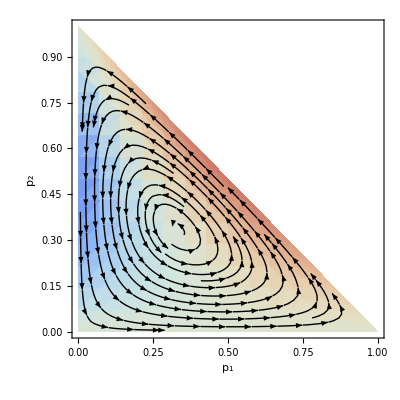

```mathematica
Show[fig1dp, fig1s]
```

### Custom streamDensityPlot (Supporting Code)

```mathematica
streamDensityPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=(* Created by Jens U.Nöckel for Mathematica 8, updated by @Locus_of_ctrl for StreamPlot 01/2019 *)Module[{img,cont,pL,p,plotRangeRule,densityOptions,streamOptions,frameOptions,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[DensityPlot],Except[{ImageSize,Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,ImagePadding->None,Frame->None,Axes->None}];
pL=DensityPlot[f,rx,ry,Evaluate@Apply[Sequence,densityOptions]];
p=First@Cases[{pL},Graphics[__],∞];
plotRangeRule=FilterRules[Quiet@AbsoluteOptions[p],PlotRange];
streamOptions=Join[FilterRules[{opts},FilterRules[Options[StreamPlot],Except[{Prolog,Epilog,FrameTicks,Background,Frame,Axes}]]],{Frame->None,Axes->None}];
(* The density plot img and stream plot cont are created here:*)img=Rasterize[p,"Image", Background->None];
cont=If[MemberQ[{0,None},(streams/.FilterRules[{opts},streams])],{},StreamPlot[f,rx,ry,Evaluate@Apply[Sequence,streamOptions]]];
(* Before showing the plots,set the PlotRange for the frame which will be drawn separately: *)frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
(* To align the image img with the stream plot,enclose img in a bounding box rectangle of the same dimensions as cont,
and then combine with cont using Show: *)
(* @Locus_of_crrl: Instead of setting alpha channel inside Show[],
I use Background->None in Rasterize[], which adds alpha channel automatically *) 
If[Head[pL]===Legended,Legended[#,pL[[2]]],#]&@Show[Graphics[{Inset[Show[img,AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],cont,Evaluate@Apply[Sequence,frameOptions]]]
```

### Custom streamDensityPlot

This should give 7-10x more compact vector image output on export compared to built-in

```mathematica
streamDensityPlot[{X,Y}, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], ColorFunction->(ColorData["ThermometerColors"][#1+.5]&),ColorFunctionScaling->False,FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12}, StreamStyle->Black, StreamScale->0.1]
```

-Graphics-

### Ternary Diagram (Supporting Code)

```mathematica
ClearAll[tickGraphics,triangleTicks];
Module[{ticklen=0.025,(*length of ticks (const parameter)*)textoffset=0.04},tickGraphics[tickrange:{0.,total_},angle_]:=With[{rotSideXF=RotationTransform[angle,total {1.,Tan[Pi/6]}/2.]},{Line[rotSideXF/@Thread[{tickrange,0}]],With[{rotTickXF=Composition[RotationTransform[π/3.,rotSideXF@{#,0.}],rotSideXF]},{Text[NumberForm[N@#,{3,2}],rotTickXF[total {-ticklen-textoffset,0}+{#,0.}],{0,0.}],{Line[rotTickXF/@{total {-ticklen,0}+{#,0.},{#,0.}}]}}]&/@Select[N@FindDivisions[tickrange,4],0.≤#≤total&]}];
triangleTicks[g_Graphics,total_: 1]:=Show[Graphics[First@g],Graphics[{AbsoluteThickness[0.5],Table[tickGraphics[{0.,total},N@angle],{angle,0,4 Pi/3,2 Pi/3}]}],Axes->False,Frame->None,PlotRange->total {{0,1+ticklen},{0,Sqrt[3]/2+ticklen/2}},PlotRangePadding->0.07 total,PlotRangeClipping->False,ImagePadding->{{20,5},{20,5}}]]
```

```mathematica
{error,xf}=FindGeometricTransform[{{0,0},{1,0},{1,Tan[Pi/3]}/2},{{0,0},{1,0},{0,1}}];
```

```mathematica
Options[ternaryForm]={axisLabels->{"p_1","p_2","p_3"}}
```

{axisLabels→{p_1,p_2,p_3}}

```mathematica
ternaryForm[x_,OptionsPattern[]] := Show[triangleTicks[Graphics[GeometricTransformation[First@x,xf]]], Graphics[{Text[OptionValue[axisLabels][[1]],{0.5,-0.12}],Rotate[Text[OptionValue[axisLabels][[3]],{0.1,0.45}],60 Degree],Rotate[Text[OptionValue[axisLabels][[2]],{0.9,0.45}],-60Degree]}]]
```

### Ternary Diagram

Repeating the above plot except without the frame:

```mathematica
dp = streamDensityPlot[{X,Y}, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], ColorFunction->(ColorData["ThermometerColors"][#1+.5]&),ColorFunctionScaling->False,Frame->None, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12}, StreamStyle->Black,StreamScale->0.1];
```

```mathematica
ternaryForm[dp, axisLabels->{"Hawk", "Dove", "Bourgeois"}]
```

-Graphics-

The figures below were labeled using axisLabels option of ternaryForm[], which takes a list of text strings:

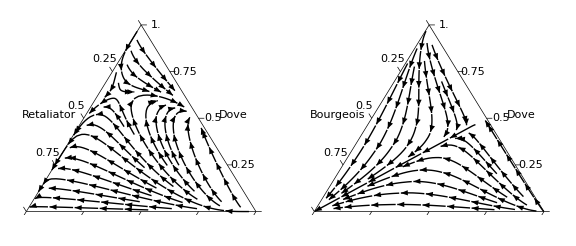

```mathematica
GraphicsRow[{-Graphics-,-Graphics-}, ImageSize->Large,Spacings->0]
```

In the instances below, I set StreamPoints option to 5 and 10, respectively, to avoid unnecessarily busy plots:

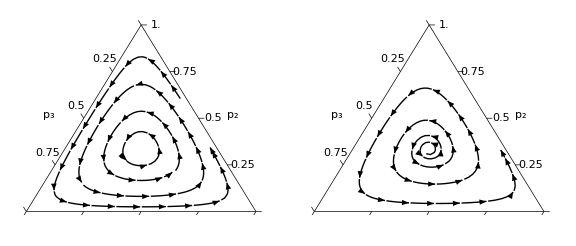

```mathematica
GraphicsRow[{-Graphics-,-Graphics-}, ImageSize->Large,Spacings->0]
```

## Time Series Plot

There is a connection between replicator models and Lotka-Volterra equations; results should be similar.

```mathematica
repl2 = {Subscript[p, 1]-> x[t], Subscript[p, 2]-> y[t]};
```

```mathematica
lv=With[{x0=.5,y0=.1, n=30},NDSolve[{x'[t]==X/.repl2,y'[t]==Y/.repl2,x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,n}]]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

```mathematica
oyb = {ColorData[97,"ColorList"][[4]], ColorData[97,"ColorList"][[2]], ColorData[97,"ColorList"][[1]]};
```

```mathematica
Plot[Evaluate[{x[t],y[t],1-x[t]-y[t]}/.lv],{t,0,30},PlotLabels->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]], Defer[Subscript[p, 3]]},PlotStyle->oyb,BaseStyle->{FontSize->12}, AxesLabel->Automatic, AxesStyle->Directive[Gray, Thickness[0.002],FontColor->Black]]
```

-Graphics-